DW ljuska normalne matrice A je konveksna ljuska točaka (a_i, |a_i|^2), gdje su a_i svojstvene vrijednosti od A

```mathematica
a = {Exp[I π/4], Exp[I 3*π/4], Exp[-I π/4], Exp[-I 3*π/4], 
Sqrt[2]*Exp[I π/4], Sqrt[2]*Exp[I 3*π/4], Sqrt[2]*Exp[-I π/4], Sqrt[2]*Exp[-I 3*π/4]};
A = DiagonalMatrix[a];
ConvexHullMesh[
Table[
{Re[a[[k]]], Im[a[[k]]], Abs[a[[k]]]^2},
{k, 1, Length[a]}
], PlotTheme -> "Detailed"
]
```

-Graphics3D-

DW ljuska nilpotentne matrice reda 2

```mathematica
DWVisualRandom[{{0, 1}, {0, 0}}]
```

-Graphics3D-

```mathematica
DWVisualRandom[{{0, 1, 1}, {0, 0, 1}, {0, 0, 0}}, 10000]
```

-Graphics3D-

```mathematica
B = {{0, 1, 1}, {0, 0, 1}, {0, 0, 0}};
```

```mathematica
Norm[B - 2 IdentityMatrix[3]] == Norm[B + 2 IdentityMatrix[3]]
```

False

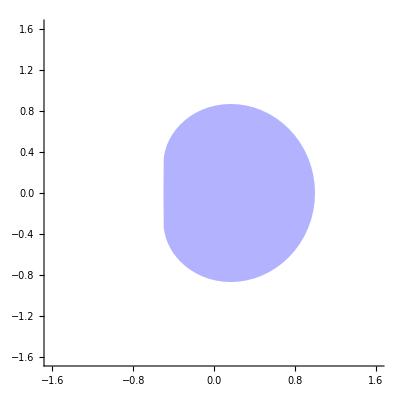

```mathematica
NumericalRangeVisual[B]
```